## Resolución del sistema

```mathematica
Clear[alphaMas, alphaMenos, alphaZ, Ω, β]
```

```mathematica
β = 0.1; Ω1 = 0.4;γ=0.0035;Ω=Ω1-I γ;
```

```mathematica
{alphaMas, alphaZ, alphaMenos}=NDSolveValue[{x'[t]-  2y'[t] x[t] + (I Ω)/2(1 + x[t]^2)== 0 ,y'[t] == I/2(Ω x[t] - (β^2 )t),z'[t]Exp[-2 y[t]]+ (I Ω)/2 == 0, x[-150]==y[-150]==z[-150]== 0},{x,y, z},{t,-250, 250},AccuracyGoal->10, PrecisionGoal->10];
```

```mathematica
alphaMasInterp = Interpolation[Table[{t, alphaMas[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaMenosInterp = Interpolation[Table[{t, alphaMenos[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

```mathematica
alphaZInterp = Interpolation[Table[{t,alphaZ[t]},{t,-220,200,0.005}], InterpolationOrder->5];
```

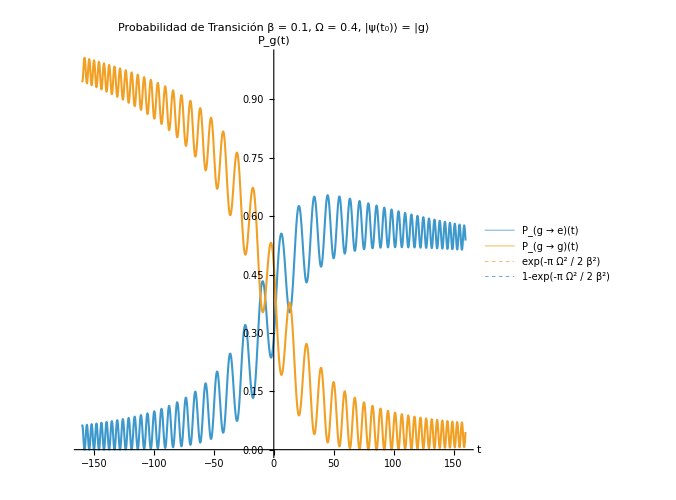

```mathematica
Plot[{(Abs[alphaMasInterp[t]]^2 )Exp[-2Re[alphaZInterp[t]]], Abs[Exp[- alphaZInterp[t]] ]^2,Exp[-π(Ω^2/(2(β^2)))], 1- Exp[-π(Ω^2/(2β^2))]}, {t, -160, 160}, FrameTicksStyle->{{20,2},{20,20}}, PlotStyle->{Thickness[0.003], Thickness[0.003], Directive[Dashed, Thickness[0.002], Orange, Opacity[0.85]], Directive[Dashed, Thickness[0.002], RGBColor[0,0.45,0.8], Opacity[0.85]]},PlotLegends-> {"P_(g → e)(t)", "P_(g → g)(t)","exp(-π Ω^2 / 2 β^2)","1-exp(-π Ω^2 / 2 β^2)"},AxesLabel-> {Style["t",14,GrayLevel[0.26]] , Style["P_g(t)",13, GrayLevel[0.26]]},AspectRatio->1, ImageSize->500,
PlotLabel->Style["Probabilidad de Transición  β = 0.1, Ω = 0.4, |ψ(t_0)⟩ = |g⟩ ", 18, FontFamily->"Times New Roman", Black]]
```

INTEGRALES

```mathematica
I1[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2 alphaZInterp[t]]alphaMenosInterp[t]^2, {t,T0 , T}, MaxRecursion->20]]^2
```

```mathematica
I2[Γ_, ω_, T_, T0_]:= Abs[NIntegrate[-Exp[(Γ-I ω)t]Exp[-2alphaZInterp[t]]alphaMenosInterp[t],{t,T0,T}, MaxRecursion->20]]^2
```

```mathematica
S[Γ_,ω_,T_, T0_]:=2Γ Exp[-2Γ T](I1[Γ, ω,T, T0]+I2[Γ, ω,T,T0])
```

```mathematica
SBas[ω_] := ((Ω/Ωr)^2)((Γ (1-Δ/Ωr))/(4 (Γ^2 +(ω-ν-Ωr)^2))+(1/2 Γ)/(Γ^2 + (ω-ν)^2)+(Γ (1+Δ/Ωr))/(4 (Γ^2+(ω-ν+Ωr)^2))) ;
```

```mathematica
SExc[ω_] := (Γ/8((1+(Δ/Ωr)^2-2(Δ/Ωr))(Ω/Ωr)^2 +(1-Δ/Ωr)^4))/(Γ^2 +(ω-ν-Ωr)^2)+(Γ/2(((Δ/Ωr)^2)((Ω/Ωr)^2) +(1-Δ^2/Ωr^2)^2))/(Γ^2 + (ω-ν)^2)+(Γ/8((1+(Δ/Ωr)^2+2(Δ/Ωr))(Ω/Ωr)^2 +(1+Δ/Ωr)^4))/(Γ^2+(ω-ν+Ωr)^2);
```

```mathematica
T0=-200;T = 80;Γ = 0.1;ν=2.2; Ωr = Sqrt[ (T*β^2)^2+ Ω^2];Δ=-T*β^2;
```

```mathematica
ωmin = (ν-2.2)/ν;ωmax = (ν+2.2)/ν;
```

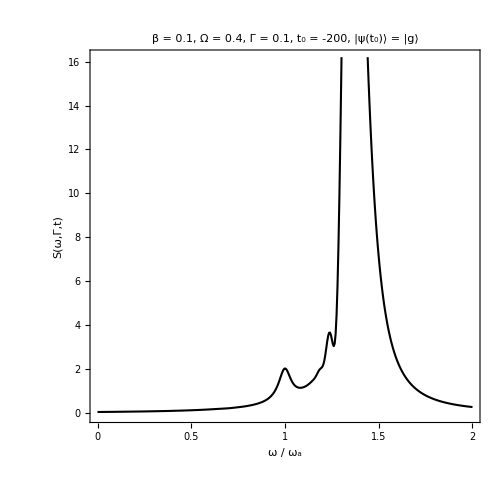

```mathematica
Show[{ListLinePlot[ParallelTable[{ω,S[Γ,ω*ν -ν,T,T0]},{ω,ωmin,ωmax,(ωmax-ωmin)/400}],PlotRange->{-0.1,16.2},Joined->True,AxesOrigin->None,
Frame->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,FrameLabel->{Style["ω / ω_a",16,FontFamily->"Times New Roman",Gray],Style["S(ω,Γ,t)",16,FontFamily->"Times New Roman",Gray]},
 ImageSize->500,PlotLabel->Style["β = 0.1, Ω = 0.4, Γ = 0.1, t_0 = -200, |ψ(t_0)⟩ = |g⟩", 16, FontFamily->"Times New Roman", Black]],ListLinePlot[ParallelTable[{ω,SBas[ω*ν]},{ω,ωmin,ωmax,(ωmax-ωmin)/400}],Joined->True,AxesOrigin->None,PlotRange->{-0.1,16.6},
Frame->True,Axes->False,PlotStyle->Directive[Darker[Red],Thickness[0.004], Opacity[0.4]],FrameTicksStyle->{{14,2},{14,20}},PlotRangePadding->0,AspectRatio->1,ImageSize->500]},FrameTicks->{{{0,2,4,6,8,10,12,14,16},None},{{0,0.5,1,1.5,2},None}}]
```